# Muon Production in SM - e^-e^+-> μ^- μ^+

## Load FeynArts and FormCalc

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts-3.11/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc-9.10/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Quit[]
```

## Tree-Level

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

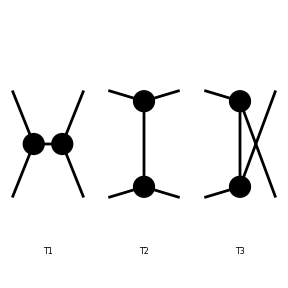

```mathematica
tmp=CreateTopologies[0,2->2,Adjacencies->3];
Paint[tmp];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 2: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 3: 0 Generic, 0 Classes, 0 Particles insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

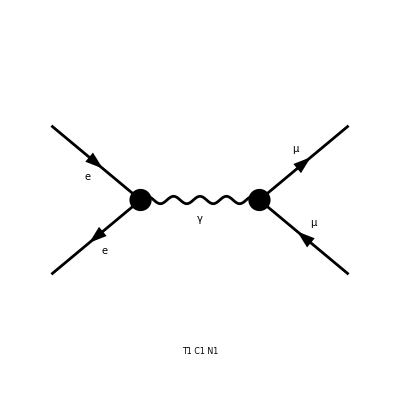

```mathematica
imp=InsertFields[tmp, {F[2,{1}], -F[2,{1}]} -> {F[2,{2}], -F[2,{2}]},InsertionLevel->Particles,QEDOnly];
Paint[imp, PaintLevel->{Classes}];
```

```mathematica
ampmp=CreateFeynAmp[imp,AmplitudeLevel->{Particles}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

FeynAmpList[Process→{{F[2,{1}],p1,ME,{-Charge,LeptonNumber}},{-F[2,{1}],p2,ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}},{-F[2,{2}],k2,MM,{Charge,-LeptonNumber}}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{S,-F[1],F[1],-F[1,{1}],F[1,{1}],-F[1,{2}],F[1,{2}],-F[1,{3}],F[1,{3}],Mix[S,V],S[1],S[2],-S[3],S[3],-U[2],U[2],-U[3],U[3],-U[4],U[4],V[2],-V[3],V[3],Mix[S,V][2],-Mix[S,V][3],Mix[S,V][3],Rev[S,V][2],-Rev[S,V][3],Rev[S,V][3]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[],v̄[p2,ME].(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).u[p1,ME] ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).v[k2,MM] g[Lor1,Lor2] 1/(k1+k2)^2]]

```mathematica
ClearProcess[]
```

```mathematica
rampmp=CalcFeynAmp[ampmp]
```

preparing FORM code in /home/riccardo/fc-amp-4.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-8 Alfa π Sub1 Den[S,0]]

## One-Loop

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cedg/ehfgfhgh.m, 0 diagrams

> Top. 3 aebf/cfdg/fhegehgh.m, 0 diagrams

> Top. 4 aebf/cgde/ehfgfhgh.m, 0 diagrams

> Top. 5 aebf/cgdf/fhegehgh.m, 0 diagrams

> Top. 6 aebf/cgdg/ghefehfh.m, 0 diagrams

> Top. 7 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 8 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 9 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 10 aebe/cfdf/egfhghgh.m, 0 diagrams

> Top. 11 aebe/cfdg/effhghgh.m, 0 diagrams

> Top. 12 aebe/cfdg/egghfhfh.m, 0 diagrams

> Top. 13 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 14 aebf/cedg/effhghgh.m, 0 diagrams

> Top. 15 aebf/cedg/egghfhfh.m, 0 diagrams

> Top. 16 aebf/cfde/egfhghgh.m, 0 diagrams

> Top. 17 aebf/cfdg/efehghgh.m, 0 diagrams

> Top. 18 aebf/cfdg/fggheheh.m, 0 diagrams

> Top. 19 aebf/cgde/effhghgh.m, 0 diagrams

> Top. 20 aebf/cgde/egghfhfh.m, 0 diagrams

> Top. 21 aebf/cgdf/efehghgh.m, 0 diagrams

> Top. 22 aebf/cgdf/fggheheh.m, 0 diagrams

> Top. 23 aebf/cgdg/egehfhfh.m, 0 diagrams

> Top. 24 aebf/cgdg/fgfheheh.m, 0 diagrams

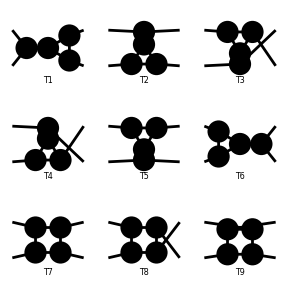

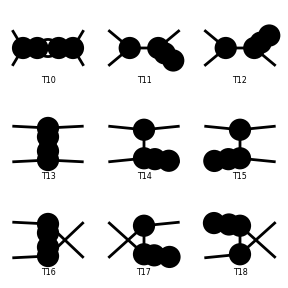

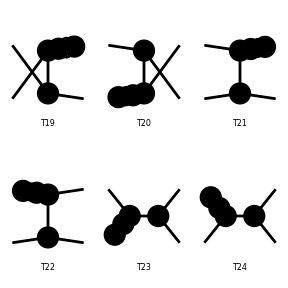

```mathematica
tmp1=CreateTopologies[1,2->2, Adjacencies->3,ExcludeTopologies->{Tadpoles}];
Paint[tmp1];
```

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 2: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 3: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 4: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 5: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 6: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 7: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 8: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 9: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 10: 1 Generic, 3 Classes, 9 Particles insertions

> Top. 11: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 12: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 13: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 14: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 15: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 16: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 17: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 18: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 19: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 20: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 21: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 22: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 23: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 24: 1 Generic, 1 Classes, 1 Particles insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 9 Generic, 11 Classes, 17 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

> Top. 3 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 4 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 5 aebe/cfdf/egfhghgh.m, 0 diagrams

> Top. 6 aebe/cfdg/effhghgh.m, 0 diagrams

> Top. 7 aebe/cfdg/egghfhfh.m, 0 diagrams

> Top. 8 aebf/cgdg/egehfhfh.m, 0 diagrams

> Top. 9 aebf/cgdg/fgfheheh.m, 0 diagrams

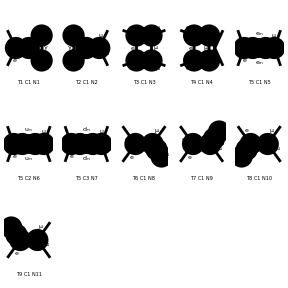

```mathematica
imp1=InsertFields[tmp1,{F[2,{1}], -F[2,{1}]} -> {F[2,{2}], -F[2,{2}]}, InsertionLevel->Particles,QEDOnly];
Paint[imp1,PaintLevel->{Classes}, ColumnsXRows->{5,5}];
```

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

> Top. 5 aebf/cedf/ef.m, 0 diagrams

> Top. 6 aebe/cfdf/ef.m, 0 diagrams

> Top. 7 aebe/cfdf/gegf.m, 0 diagrams

> Top. 8 aebe/cfdg/gfef.m, 0 diagrams

> Top. 9 aebe/cfdg/fgeg.m, 0 diagrams

> Top. 10 aebf/cedf/gegf.m, 0 diagrams

> Top. 11 aebf/cedg/gfef.m, 0 diagrams

> Top. 12 aebf/cfde/gegf.m, 0 diagrams

> Top. 13 aebf/cfdg/geef.m, 0 diagrams

> Top. 14 aebf/cgde/gfef.m, 0 diagrams

> Top. 15 aebf/cgdf/geef.m, 0 diagrams

> Top. 16 aebf/cedg/fgeg.m, 0 diagrams

> Top. 17 aebf/cgde/fgeg.m, 0 diagrams

> Top. 18 aebf/cgdg/feeg.m, 0 diagrams

> Top. 19 aebf/cfdg/egfg.m, 0 diagrams

> Top. 20 aebf/cgdf/egfg.m, 0 diagrams

> Top. 21 aebf/cgdg/effg.m, 0 diagrams

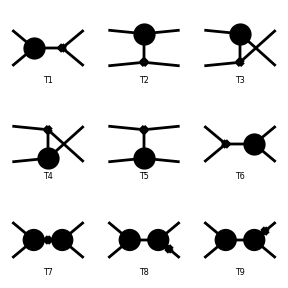

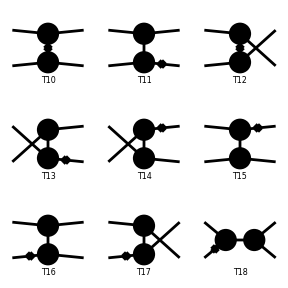

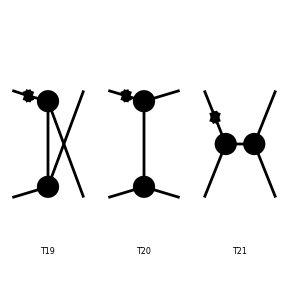

```mathematica
tctmp=CreateCTTopologies[1,2->2, Adjacencies->3,ExcludeTopologies->{TadpoleCTs}];
Paint[tctmp];
```

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 2: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 3: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 4: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 5: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 6: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 7: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 8: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 9: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 10: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 11: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 12: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 13: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 14: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 15: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 16: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 17: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 18: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 19: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 20: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 21: 1 Generic, 1 Classes, 1 Particles insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 7 Generic, 7 Classes, 7 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

> Top. 4 aebe/cfdg/gfef.m, 0 diagrams

> Top. 5 aebe/cfdg/fgeg.m, 0 diagrams

> Top. 6 aebf/cgdg/feeg.m, 0 diagrams

> Top. 7 aebf/cgdg/effg.m, 0 diagrams

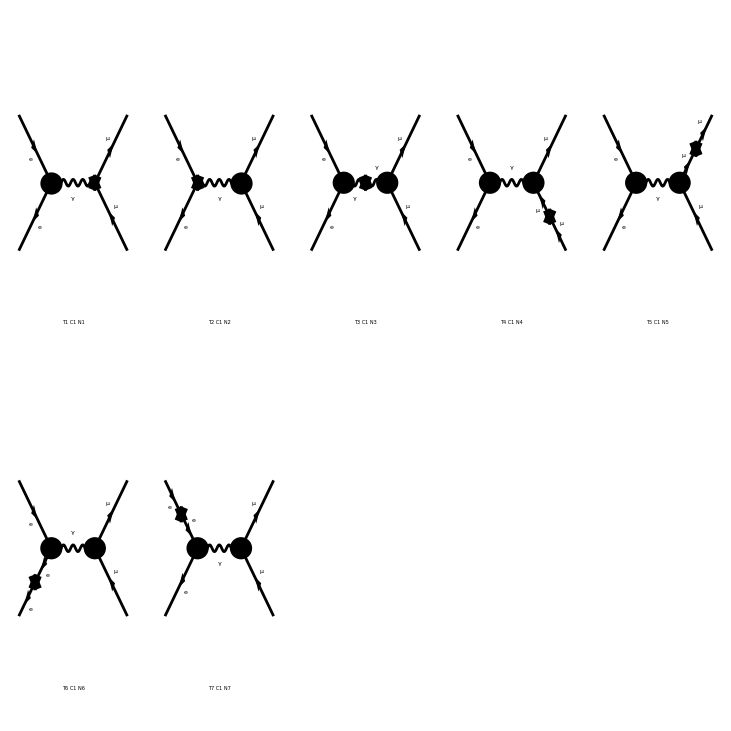

```mathematica
ictmp=InsertFields[tctmp,{F[2,{1}], -F[2,{1}]} -> {F[2,{2}], -F[2,{2}]}, InsertionLevel->Particles,QEDOnly];
Paint[ictmp,PaintLevel->{Classes}, ColumnsXRows->{5,5}];
```

```mathematica
ampmp1=CreateFeynAmp[imp1];
```

creating amplitudes at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 2: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 3: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 4: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 5: 1 Generic, 3 Classes, 9 Particles amplitudes

> Top. 6: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 7: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 8: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 9: 1 Generic, 1 Classes, 1 Particles amplitudes

in total: 9 Generic, 11 Classes, 17 Particles amplitudes

```mathematica
rampmp1=CalcFeynAmp[ampmp1]
```

preparing FORM code in /home/riccardo/fc-amp-4.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-Alfa2 (-24 (F1 F2+F3 F4) D0i[dd00,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-8 (Sub4 D0i[dd00,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+Sub2 (D0i[dd11,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd11,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]))+4 (Sub29 (D0i[dd12,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd12,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])+Sub36 D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+Sub14 D0i[dd3,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+Sub8 D0i[dd33,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2])-4 (Sub3 (D0i[dd1,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd1,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])+Sub31 D0i[dd13,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+Sub33 D0i[dd13,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+Sub20 D0i[dd2,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+Sub18 D0i[dd2,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+Sub42 D0i[dd22,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+Sub40 D0i[dd22,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+Sub24 D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+Sub12 D0i[dd3,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+Sub37 D0i[dd33,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])-(8 ((F14+F15) (F13+F16) ME C0i[cc12,ME2,S,ME2,0,ME2,ME2]+(F10+F11) (F12+F9) MM C0i[cc12,MM2,S,MM2,0,MM2,MM2])+4 (Sub15 (C0i[cc1,ME2,S,ME2,0,ME2,ME2]+C0i[cc2,ME2,S,ME2,0,ME2,ME2])+Sub9 (C0i[cc1,MM2,S,MM2,0,MM2,MM2]+C0i[cc2,MM2,S,MM2,0,MM2,MM2])+(F14+F15) (F13+F16) ME (C0i[cc11,ME2,S,ME2,0,ME2,ME2]+C0i[cc22,ME2,S,ME2,0,ME2,ME2])+(F10+F11) (F12+F9) MM (C0i[cc11,MM2,S,MM2,0,MM2,MM2]+C0i[cc22,MM2,S,MM2,0,MM2,MM2]))+Sub1 (4 Finite-8 (B0i[bb1,S,ME2,ME2]+B0i[bb1,S,ML2,ML2]+B0i[bb1,S,MM2,MM2])-8/3 (B0i[bb1,S,MB2,MB2]+B0i[bb1,S,MD2,MD2]+B0i[bb1,S,MS2,MS2])-32/3 (B0i[bb1,S,MC2,MC2]+B0i[bb1,S,MT2,MT2]+B0i[bb1,S,MU2,MU2])-4 (B0i[bb0,S,ME2,ME2]+B0i[bb0,S,MM2,MM2]+(2 ME2-S) C0i[cc0,ME2,S,ME2,0,ME2,ME2]+(2 MM2-S) C0i[cc0,MM2,S,MM2,0,MM2,MM2])+8 (C0i[cc00,ME2,S,ME2,0,ME2,ME2]+C0i[cc00,MM2,S,MM2,0,MM2,MM2])+ME2 (8 Finite-16 B0i[bb0,ME2,0,ME2]+16 B0i[bb1,ME2,0,ME2]) Den[ME2,ME2]+MM2 (8 Finite-16 B0i[bb0,MM2,0,MM2]+16 B0i[bb1,MM2,0,MM2]) Den[MM2,MM2])) Den[S,0]+Sub1 (8 C0i[cc0,S,MM2,MM2,0,0,MM2]+4 (ME2+MM2-T) D0i[dd0,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-4 (ME2+MM2-U) D0i[dd0,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+(8 (A0[ME2]+A0[ML2]+A0[MM2])+8/3 (A0[MB2]+A0[MD2]+A0[MS2])+32/3 (A0[MC2]+A0[MT2]+A0[MU2])-16 (B0i[bb00,S,ME2,ME2]+B0i[bb00,S,ML2,ML2]+B0i[bb00,S,MM2,MM2])-16/3 (B0i[bb00,S,MB2,MB2]+B0i[bb00,S,MD2,MD2]+B0i[bb00,S,MS2,MS2])-64/3 (B0i[bb00,S,MC2,MC2]+B0i[bb00,S,MT2,MT2]+B0i[bb00,S,MU2,MU2])) Den[S,0]^2))]

```mathematica
ampctmp=CreateFeynAmp[ictmp];
```

creating amplitudes at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 2: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 3: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 4: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 5: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 6: 1 Generic, 1 Classes, 1 Particles amplitudes

> Top. 7: 1 Generic, 1 Classes, 1 Particles amplitudes

in total: 7 Generic, 7 Classes, 7 Particles amplitudes

```mathematica
ClearProcess[]
```

```mathematica
rampctmp=CalcFeynAmp[ampctmp]
```

preparing FORM code in /home/riccardo/fc-amp-4.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][Alfa π (2 Sub201-4 (Sub261 Den[ME2,ME2]+Sub231 Den[MM2,MM2])) Den[S,0]]

```mathematica
UVDivergentPart[rampmp1]
```

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-Alfa2 (-Sub1 (28 Divergence-24 Divergence ME2 Den[ME2,ME2]-24 Divergence MM2 Den[MM2,MM2]) Den[S,0]+(8 (Divergence ME2+Divergence ML2+Divergence MM2)+8/3 (Divergence MB2+Divergence MD2+Divergence MS2)+32/3 (Divergence MC2+Divergence MT2+Divergence MU2)-16 (1/12 Divergence (6 ME2-S)+1/12 Divergence (6 ML2-S)+1/12 Divergence (6 MM2-S))-16/3 (1/12 Divergence (6 MB2-S)+1/12 Divergence (6 MD2-S)+1/12 Divergence (6 MS2-S))-64/3 (1/12 Divergence (6 MC2-S)+1/12 Divergence (6 MT2-S)+1/12 Divergence (6 MU2-S))) Sub1 Den[S,0]^2)]

```mathematica
UVDivergentPart[rampctmp]
```

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][0]